```mathematica
Directory[]
```

/home/cooper-cooper

```mathematica
SetDirectory["/home/cooper-cooper/Desktop/vans/results/xxz/plot"]
```

/home/cooper-cooper/Desktop/vans/results/xxz/plot

Eigenvalues::arh: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors would be sufficient, consider restricting this number using the second argument to Eigenvalues.

General::stop: Further output of Eigenvalues::arh will be suppressed during this calculation.

xxz8.csv

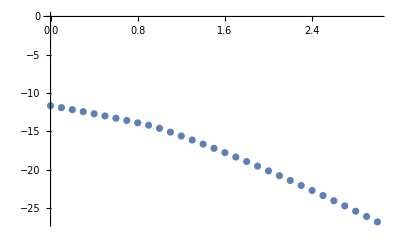

```mathematica
g=1.0;op[n_Integer,k_Integer,a_?MatrixQ]/;1≤k≤n&&Dimensions[a]=={2,2}:=KroneckerProduct[IdentityMatrix[2^(k-1),SparseArray],a,IdentityMatrix[2^(n-k),SparseArray]];
sz[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[3]];
sy[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[2]];
sx[n_Integer,k_Integer]/;1≤k≤n:=op[n,k,PauliMatrix[1]];
HH[n_Integer/;n≥3,g_,J_]:=g*Sum[sz[n,k],{k,n}]+Sum[sx[n,k].sx[n,Mod[k+1,n,1]],{k,n}] + Sum[sy[n,k].sy[n,Mod[k+1,n,1]],{k,n}] + J*Sum[sz[n,k].sz[n,Mod[k+1,n,1]],{k,n}];
js=Table[k,{k,0,3,.1}];
num =Table[J=js[[k]];kk=HH[8,1.0,J]//Eigenvalues//Min;{J,kk},{k,1,Length[js]}];
Export["xxz8.csv",num]
ListPlot[num, PlotRange->All]
```

```mathematica
Table[num[[k]][[2]], {k,Length[num]}]
```

{-11.6569,-11.9037,-12.161,-12.4279,-12.7037,-12.9879,-13.2798,-13.5789,-13.8845,-14.1963,-14.6044,-15.0983,-15.6063,-16.1284,-16.6644,-17.2142,-17.7774,-18.3538,-18.9429,-19.5444,-20.1577,-20.7823,-21.4177,-22.0632,-22.7183,-23.3823,-24.0548,-24.7352,-25.4228,-26.1173,-26.8181}

```mathematica
{-11.6569,-11.4221,-11.4572,-11.4969,-11.6,-12.,-12.8,-13.6,-14.4,-15.2,-16.,-16.8,-17.6,-18.4,-19.2,-20.,-20.8,-21.6,-22.4,-23.2,-24.,-24.8,-25.6,-26.4,-27.2,-28.,-28.8,-29.6,-30.4,-31.2,-32.}
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

{-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.}

```mathematica
Length[js]
```

20